```mathematica
delta=0.11;
a=1;
b=11;
```

```mathematica
partition=Partition[Table[i,{i,a,b,delta}],2,1];
```

```mathematica
partition⟦1;;3⟧
```

{{1.,1.11},{1.11,1.22},{1.22,1.33}}

```mathematica
varSeries={1,2,3,3.2,3.2,3.5,3.6,4,4.1,4.5,5.4,6.1,7.1,7.3,7.4,8.3,9,10,10.1};
counts=ConstantArray[0,Length@partition];
```

```mathematica
Do[Do[If[partition⟦j,1⟧< varSeries⟦i⟧&&varSeries⟦i⟧≤ partition⟦j,2⟧,counts⟦j⟧++],{j,1,Length@partition}],{i,1,Length@varSeries}]
```

```mathematica
counts
```

{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,2,0,0,1,1,0,0,0,1,1,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,1,1,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,1,0,0,0,0,0,0,0}

```mathematica
frequency=counts/delta;
```

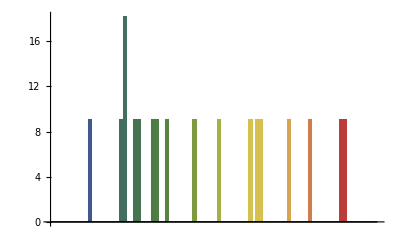

```mathematica
BarChart[frequency,ChartStyle->"DarkRainbow"]
```